## Here I just check and experiment with Discrete Fourier transform done by three methods : Mathematica' s inbuild Fourier, my manual implementation and a naive approximation of the Fourier integral transform

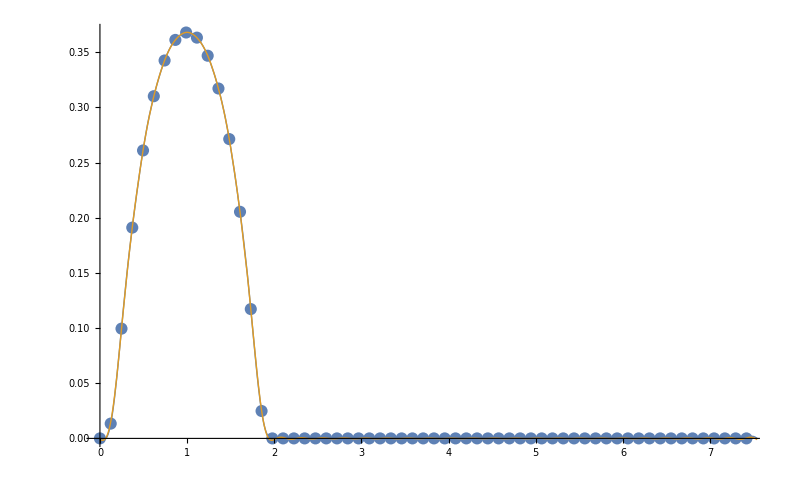

```mathematica
ClearAll[b]
$Assumptions={n ∈Integers, m ∈Integers};
(*Signal*)
b[τ_]= E^(- 1/(1.0000001-(τ-1)^2)) HeavisideTheta[τ]HeavisideTheta[2-τ];
r=-3.;
(*b[τ_] = DiracDelta[r-τ];*)

(*Time period*)
T=4.; 
(*Number of fourier components*)
NN=30; Maxω = 25;
T= 2 π NN/Maxω;δω = Maxω/NN;
(*Time range*)
dt = T 1/(2NN+1);
rngt = Range[0,T (2NN)/(2NN+1) ,dt];
bN = b/@rngt//Chop;

(*Manual implementation of mathematica Fourier*)
(*v[n_]= ⅇ^(-2 π ⅈ (# n)/(2 NN+1))ⅇ^(2 π ⅈ #NN/(2 NN+1))&/@ Range[0,2NN];
c = (T/(2 NN +1)bN.Conjugate[v[#+NN]])&/@Range[-NN,NN] //Simplify//Chop;*)

v[n_]= ⅇ^(-2 π ⅈ (# n)/(2 NN+1))&/@ Range[0,2NN];
c = T/(2 NN +1)bN.Conjugate[v[#]]&/@Range[-NN,NN] //Simplify//Chop;

(*Frequency range*)
rngωFourier=Range[-Maxω,Maxω,δω];
    (*δt ==  (2 π)/((2NN+1)δω) == T/(2NN+1)⟹ T ==  (2π)/δω*) 

(*what to do to Mathematica Foureir so that the result is a list of the components of rngω*)
Mbω=T/(√(2 NN+1))Fourier[bN];
Mbω= (#[[2]]~Join~#[[1]])&@TakeDrop[Mbω,NN+1];

(*My veriosn of Fourier*)
ListPlot[{{rngωFourier,Re@c}ᵀ,{rngωFourier,Im@c}ᵀ},PlotRange->All,Joined->True];

(*Reconstruct original signal from my veriosn of Fourier, brutal Fourier Transform and compare*)
listbω=NIntegrate[b[t]E^(I # t),{t,0.,T}]&/@rngωFourier;
(*listbω=Integrate[b[t]E^(I ω t),{t,0.,T}]/.ω-># &/@rngωFourier;*)

bc[t_] = 1./(2π) c.Exp[-I t rngωFourier ] δω;
bNF[t_] = 1./(2π) listbω.Exp[-I t rngωFourier ] δω;
p1= Plot[{(*Re@(b[t]),*)Re@bc[t],Re@bNF[t]},{t,0,T},PlotRange->All,PlotStyle-> {Thick,Thick}];
Show[ ListPlot[{rngt,bN}ᵀ],p1]
(*(*frequency of brutal Fourier Transform*)
ListPlot[{{rngω,Re@( listbω )}ᵀ,{rngω,Im@( listbω )}ᵀ},PlotRange->All,Joined->True,PlotLabel->"listbω"]
ListPlot[{{rngω,Re@( listbω - c)}ᵀ,{rngω,Im@( listbω - c)}ᵀ},PlotRange->All,Joined->True]*)

(*ListPlot[{{rngω,Re@(c- Mbω)}ᵀ,{rngω,Im@(c-Mbω)}ᵀ},PlotRange->All,Joined->True,PlotLabel->"Re@(c- Mbω)"]*)
(*ListPlot[{{rngω,Re@(Mbω)}ᵀ,{rngω,Im@(Mbω)}ᵀ},PlotRange->All,Joined->True]*)
```

628.319

-30.

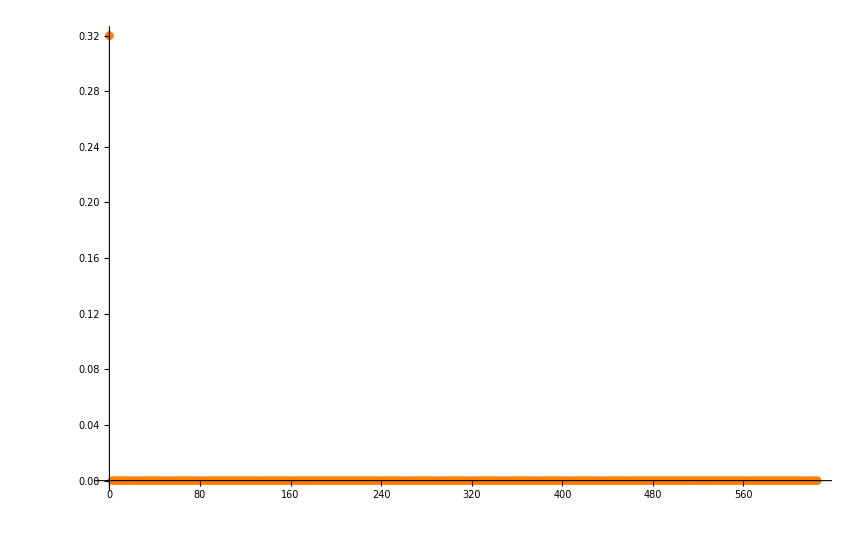

{0.0980055,-0.0964831,0.095256,-0.0943067,0.0936219,-0.0931923,0.0930122,-0.0930791,0.093394,-0.093961,0.0947879,-0.0958859,0.0972707,-0.0989623,0.100986,-0.103375,0.106167,-0.109413,0.113173,-0.117523,0.12256,-0.128403,0.135207,-0.143174,0.152568,-0.163747,0.1772,-0.193622,0.214023,-0.23994,0.273826,-0.319845,0.385686,-0.487287,0.663953,-1.04593,2.47823,6.66083,-1.42171,0.796964,-0.554688,0.426241,-0.346844,0.293036,-0.254265,0.225081,-0.202389,0.184297,-0.169587,0.157438,-0.147278,0.138695,-0.131387,0.125126,-0.119737,0.115086,-0.111066,0.107593,-0.1046,0.102032,-0.0998458}

```mathematica
(*Tests for using a discrete delta (plane wave delta)*)
NN=100; Maxω = 1.;
T= 2 π NN/Maxω
δω = Maxω/NN;
(*Time range*)

r = -30.;
dt = T 1/(2NN+1); 
rngt = Range[0,T (2NN)/(2NN+1) ,dt];

If[0≤ r<T,
p =  Position[Thread[Abs[r-rngt]<dt],True];
p =First@@p; (*r = rngt[[p]]*)
,
(*p =  Position[Thread[Abs[-r-rngt]<dt],True];
p =First@@p;
r =- rngt[[p]];*)
p={}
];
r
(*Known frequency response*)
δω=Maxω/NN //N;
rngω=Range[0,Maxω,δω];
 
rngωFourier=rngω~Join~Reverse@Drop[-rngω,1];

Mbω =1. +0. Exp[I r rngωFourier];

(*Known time response*)
bN = 0.*rngt; 
bN[[p]] = 1/dt;
ListPlot[{rngt,bN}ᵀ];

(* Compare inverse Fourier with known time response*)
ListPlot[{{rngt,bN}ᵀ,{rngt,√(2 NN+1)/T InverseFourier[Mbω]}ᵀ},PlotRange-> All,PlotStyle -> {{PointSize[Large]},{Orange}}]
```

## How to use the fast discrete Fourier transform 1/(√n)∑_(r=1)^n u_r e^(2π i(r-1)(s-1)/n) of Mathematica :

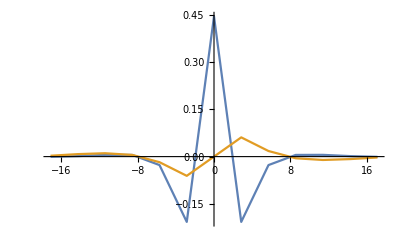

-Graphics-

```mathematica
(*MbN = ( b[(# T)/(2 NN +1)](*ⅇ^(- 2 π ⅈ # NN/(2 NN+1))*))&/@Range[0,2NN]//Chop; 
bN = ( b[#](*ⅇ^(- 2 π ⅈ # NN/(2 NN+1))*))&/@rngt//Chop; *)

listbω=T/(√(2 NN+1))Fourier[bN];
listbω= listbω[[NN+2;;All]]~Join~listbω[[1;;NN+1]];

(*Mv[n_]= ⅇ^(-2 π ⅈ (# n)/(2 NN+1))&/@ Range[0,2NN];*)
(*Mc = (1/(√(2 NN +1))MbN.Conjugate[Mv[#]])&/@Range[0,2NN] //Simplify//Chop;*)

ListPlot[{{rngω,Re@listbω}ᵀ,{rngω,Im@listbω}ᵀ},Joined->True,PlotRange->Full]
(*ListPlot[{{rngω,Re@Mc}ᵀ,{rngω,Im@Mc}ᵀ},PlotRange->{-0.1,0.4}]*)
ListPlot[{{rngω,Re@c}ᵀ,{rngω,Im@c}ᵀ},Joined->True,PlotRange->Full]
```

```mathematica
Range[1,2NN+1][[NN+1;;All]]
```

Part::span: 7 ;; (All : 1 ;; 6) is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

{1,2,3,4,5,6,7,8,9,10,11,12,13}⟦7;;(All:1;;6)⟧

```mathematica
ListPlot[{{rngω,Re@MbN}ᵀ,{rngω,Im@MbN}ᵀ},Joined->True]
```

{9.73532×10^-6,0.0000237754,0.0000356881,0.0000418687,0.0000385764,0.000022145,0.0000107835,0.0000571343,0.000111833,0.000160016,0.000178303,0.000136115,2.56728×10^-6,0.000243521,0.000584405,0.00093723,0.0011106,0.000770712,0.000552763,0.00333348,0.00757171,0.011397,0.0069793,0.0331241,0.220032,0.452874,0.220032,0.0331241,0.0069793,0.011397,0.00757171,0.00333348,0.000552763,0.000770712,0.0011106,0.00093723,0.000584405,0.000243521,2.56728×10^-6,0.000136115,0.000178303,0.000160016,0.000111833,0.0000571343,0.0000107835,0.000022145,0.0000385764,0.0000418687,0.0000356881,0.0000237754,9.73532×10^-6}